# UniDyn--Demo-Scratch.nb

John A. Marohn
jam99@cornell.edu
Cornell University

Abstract:  This demonstration notebook loads the UniDyn package and executes the package’s unit tests.

## Set the path to the package

Tell Mathematica the path to the directory containing the package.    

EDIT THE FOLLOWING PATH STRING:

```mathematica
$UniDynPath ="C:\\Users\\as836\\Documents\\GitHub\\UniDyn\\unidyn"; 
$UniDynPath="/Users/jam99/Dropbox/MarohnGroup__Software_Library/UniDyn/unidyn";
```

YOU SHOULD NOT NEED TO EDIT ANYTHING FROM HERE ONWARDS.

## Load the package and run the unit tests

### Load UniDyn

Append the package path to the system path and load the package.  Setting the global $VerboseLoad variable to True will print out the help strings for key commands in the package.

```mathematica
$Path = AppendTo[$Path,$UniDynPath];
$VerboseLoad =True; (* Set to load quietly *)
Needs["UniDyn`"]
```

### Carry out the units tests

Set the working directory to the package directory.  Get the names of all the unit-testing files included with the package, following my convention that the unit testing file end in “-tests.m”.   Carry out the tests.  Running the tests takes a few seconds, so be patient.

```mathematica
SetDirectory[$UniDynPath];
fn = FileNames["*-tests.m"];
test$report =TestReport /@ fn;
TableForm[Table[test$report[[k]],{k,1,Length[test$report]}]]
```

TestReportObject[…]
TestReportObject[…]
TestReportObject[…]
TestReportObject[…]
TestReportObject[…]
TestReportObject[…]

## Quantum optics

### Operators

```mathematica
Clear[H,Ix, Iy, Iz,Δ,ω, g, F, aL,aR,Q$sym, P$sym, Q,P,QP$rules]
CreateScalar[{Δ,ω,Δω,g, F,ϕ}];
CreateOperator[{{Ix, Iy, Iz},{aL,aR}}];
SpinSingle$CreateOperators[Ix, Iy, Iz, 1/2];
OscSingle$CreateOperators[aL,aR];

Q$sym=(aR+aL)/Sqrt[2];
P$sym =I (aR-aL)/Sqrt[2];
QP$rules = {aR -> (Q - I P)/Sqrt[2], aL -> (Q + I P)/Sqrt[2]};
```

SpinSingle$CreateOperators::nocreate: Spin operators already exist.

SpinSingle$CreateOperators::comm: Adding spin commutations relations.

SpinSingle$CreateOperators::simplify: Angular momentum L = 1/2. Adding operator simplification rules.

OscSingle$CreateOperators::nocreate: Oscillator operators already exist.

OscSingle$CreateOperators::comm: Adding oscillator commutations relations.

```mathematica
Q$sym /. QP$rules // Simplify
P$sym /. QP$rules // Simplify
```

Q

P

### Hamiltonians

#### Free evolution

```mathematica
$Assumptions = {Element[ω, Reals], ω > 0};
H$0 = ω/2 (Mult[aR,aL] + Mult[aL,aR]);
```

```mathematica
Simplify[Evolver[H$0,t,Q$sym]  /. QP$rules] // ExpToTrig // Simplify
```

Q Cos[t ω]-P Sin[t ω]

#### Position or momentum kick

```mathematica
Clear[δx,δp];
$Assumptions = {Element[δx, Reals],Element[δp, Reals]};
H$0$x$kick = δx P$sym ;
H$0$p$kick = δp Q$sym;
```

```mathematica
Simplify[Evolver[H$0$x$kick ,t,Q$sym]  /. QP$rules ~Join~ {t-> 1}]  // Simplify
Simplify[Evolver[H$0$p$kick ,t,P$sym]  /. QP$rules ~Join~ {t-> 1}]  // Simplify
```

Q-δx

P+δp

#### Phase Kick

```mathematica
$Assumptions = {Element[ω, Reals], ω > 0};
H$0$phase$kick = (ω+Δω)/2 (Mult[aR,aL] + Mult[aL,aR]) ;
```

```mathematica
Simplify[Evolver[H$0$phase$kick,t,Q$sym]  /. QP$rules] /. {Δω-> Δϕ/t} // ExpToTrig // Simplify
```

Q Cos[Δϕ+t ω]-P Sin[Δϕ+t ω]

#### Force

```mathematica
$Assumptions = {Element[F, Reals], F > 0};
H$1 = - F Q$sym;
```

```mathematica
Simplify[Evolver[H$1,t,Q$sym] /. QP$rules ]
Simplify[Evolver[H$1,t,P$sym] /. QP$rules]
```

Q

P-F t

```mathematica
Simplify[Evolver[H$1,t,aR]]
Simplify[Evolver[H$1,t,aL]]
```

aR+(ⅈ F t)/(√2)

aL-(ⅈ F t)/(√2)

#### Force with a phase factor

```mathematica
Clear[F,ϕ];
CreateScalar[{F,ϕ}];
$Assumptions = {Element[F, Reals], F > 0, Element[ϕ, Reals]};
H$1 = F (Exp[-I ϕ] aL + Exp[I ϕ] aL );
```

```mathematica
Evolver[H$1,t,aR]
```

aR-2 ⅈ F t Cos[ϕ]

Way-out !?

```mathematica
(* Extraction of operators from an expression *)
op$extA[elem_]:=Module[{pos,ans},
pos=Position[OperatorQ/@Level[elem,1],True];
ans=Level[elem,1][[pos[[1,1]]]];
Return[ans];
]

op$ext[elem_]:=Module[{ans},
If[Dimensions[elem]==={},ans = elem,
ans = Check[op$extA[elem],If[OperatorQ@elem,elem,None]]//Quiet];
Return[ans];
]
```

```mathematica
H$new  = H$1//Expand; 
Dim$ = Dimensions[H$new][[1]];
Res$ = 0;
For[j=1,j<=Dim$,j++,
A$ = op$ext@H$new[[j]];
B$ = Evolver[A$,t,aR];
C$ = H$new[[j]]/A$;
AddTo[Res$,C$*B$];
];
Res$
```

ⅇ^(-ⅈ ϕ) F (aR-ⅈ t)+ⅇ^(ⅈ ϕ) F (aR-ⅈ t)

```mathematica
Res$  // ExpToTrig// Collect[#,{aR}]&
```

2 aR F Cos[ϕ]-2 ⅈ F t Cos[ϕ]

#### Squeezing

```mathematica
$Assumptions = {Element[Δ, Reals], Δ > 0, Element[ω, Reals], ω > 0};
```

```mathematica
Simplify[Evolver[-Δ/2 I (Mult[aR,aR] - Mult[aL,aL]),t,#]  /. QP$rules,TimeConstraint->1]& /@ {Q$sym, P$sym}
```

{ⅇ^(t Δ) Q,ⅇ^(-t Δ) P}

```mathematica
Simplify[Evolver[Δ/2 I (Mult[aR,aR] - Mult[aL,aL]),t,#]  /. QP$rules]& /@ {Q$sym, P$sym}
```

{ⅇ^(-t Δ) Q,ⅇ^(t Δ) P}

```mathematica
Expand[Simplify[ExpToTrig[Evolver[Δ/2 (Mult[aR,aR] + Mult[aL,aL]),t,#]  /. QP$rules]]]& /@ {Q$sym, P$sym}
```

{Q Cosh[t Δ]+P Sinh[t Δ],P Cosh[t Δ]+Q Sinh[t Δ]}

Let's remind ourselves what the hyperbolic functions look like

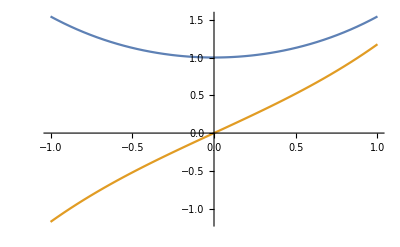

```mathematica
Plot[{Cosh[T],Sinh[T]},{T,-1,1}]
```

Free evolution plus squeezing

```mathematica
ans = Collect[Simplify[ExpToTrig[Evolver[ ω/2 (Mult[aR,aL] + Mult[aL,aR])-Δ/2 I (Mult[aR,aR] - Mult[aL,aL]),t,#]  /. QP$rules]],{Q,P}]& /@ {Q$sym, P$sym}
```

{-(P ω Sinh[t √(Δ^2-ω^2)])/(√(Δ^2-ω^2))+Q (Cosh[t √(Δ^2-ω^2)]+(Δ Sinh[t √(Δ^2-ω^2)])/(√(Δ^2-ω^2))),(Q ω Sinh[t √(Δ^2-ω^2)])/(√(Δ^2-ω^2))+P (Cosh[t √(Δ^2-ω^2)]-(Δ Sinh[t √(Δ^2-ω^2)])/(√(Δ^2-ω^2)))}

```mathematica
ans /. {ω -> 10^4,Δ-> 1} // N // Collect[#,{Q,P}]&
```

{Q (Cos[10000. t]+0.0001 Sin[10000. t])-1. P Sin[10000. t],P (Cos[10000. t]-0.0001 Sin[10000. t])+1. Q Sin[10000. t]}

## Another quantum optics example (failing)

```mathematica
Clear[λ,t, Ix, Iy, Iz,I$m, I$p,aL,aR, H];
CreateScalar[{λ,t,g}];
$Assumptions = {Element[λ, Reals], λ > 0, Element[t, Reals], t > 0, Element[g, Reals], g > 0};
CreateOperator[{{Ix, Iy, Iz,I$m,I$p},{aL,aR}}];
SpinSingle$CreateOperators[Ix, Iy, Iz, 1/2];
OscSingle$CreateOperators[aL,aR];
```

SpinSingle$CreateOperators::nocreate: Spin operators already exist.

SpinSingle$CreateOperators::comm: Adding spin commutations relations.

SpinSingle$CreateOperators::simplify: Angular momentum L = 1/2. Adding operator simplification rules.

OscSingle$CreateOperators::nocreate: Oscillator operators already exist.

OscSingle$CreateOperators::comm: Adding oscillator commutations relations.

```mathematica
I$p/:Comm[I$p,I$m]=2 Iz;
I$p/:Comm[I$p,Iz]=-I$p;
I$m/:Comm[I$m,I$p]=-2 Iz;
I$m/:Comm[I$m,Iz]=I$m;
Iz/:Comm[Iz,I$p]=I$p;
Iz/:Comm[Iz,I$m]=-I$m;
```

```mathematica
I$p/:NonCommutativeMultiply[a___,I$p,I$p,b___]:=0;
I$m/:Mult[a___,I$m,I$m,b___]:=0;

I$p/:Mult[a___,I$p,Iz,b___]:=- 1/2 Mult[a,I$p,b];
I$p/:Mult[a___,I$p,I$m,b___]:=1/2 Mult[a,b]+Mult[a,Iz,b];

I$m/:Mult[a___,I$m,Iz,b___]:= 1/2 Mult[a,I$m,b];
I$m/:Mult[a___,I$m,I$p,b___]:=1/2 Mult[a,b]-Mult[a,Iz,b];

I$z/:Mult[a___,I$z,Ip,b___]:=  1/2 Mult[a,I$p,b];
I$z/:Mult[a___,I$z,I$m,b___]:=-1/2 Mult[a,I$m,b];
```

```mathematica
Evolver[λ Iz,t,I$p]
Evolver[λ Iz,t,I$m]
```

ⅇ^(-ⅈ t λ) I$p

ⅇ^(ⅈ t λ) I$m

```mathematica
Evolver[λ Mult[I$m,aR],t,aL] // Simplify
```

aL+ⅈ I$m t λ

```mathematica
Evolver[λ Mult[I$m,aL],t,aR] // Simplify
```

aR-ⅈ I$m t λ

```mathematica
Evolver[λ Mult[Iz,aL],t,I$p]
Evolver[λ Mult[Iz, aR],t,I$m]
```

Evolver::unsolvable: Unrecognized evolution

{I$p,-ⅈ λ Mult[I$p,aL],-λ^2 Mult[I$p,aL,aL],ⅈ λ^3 Mult[I$p,aL,aL,aL],λ^4 Mult[I$p,aL,aL,aL,aL]}

Evolver::unsolvable: Unrecognized evolution

{I$m,ⅈ λ Mult[I$m,aR],-λ^2 Mult[I$m,aR,aR],-ⅈ λ^3 Mult[I$m,aR,aR,aR],λ^4 Mult[I$m,aR,aR,aR,aR]}

```mathematica
H$J = 2 I g (Mult[Iz,aR]-Mult[Iz,aL]);
Comm[H$J,I$p]
Evolver[H$J,t,I$p] // Simplify
```

2 ⅈ g (-Mult[I$p,aL]+Mult[I$p,aR])

Evolver::unsolvable: Unrecognized evolution

{I$p,-2 g (Mult[I$p,aL]-Mult[I$p,aR]),4 g^2 (Mult[I$p,aL,aL]-Mult[I$p,aL,aR]-Mult[I$p,aR,aL]+Mult[I$p,aR,aR]),-8 g^3 (Mult[I$p,aL,aL,aL]-Mult[I$p,aL,aL,aR]-Mult[I$p,aL,aR,aL]+Mult[I$p,aL,aR,aR]-Mult[I$p,aR,aL,aL]+Mult[I$p,aR,aL,aR]+Mult[I$p,aR,aR,aL]-Mult[I$p,aR,aR,aR]),16 g^4 (Mult[I$p,aL,aL,aL,aL]-Mult[I$p,aL,aL,aL,aR]-Mult[I$p,aL,aL,aR,aL]+Mult[I$p,aL,aL,aR,aR]-Mult[I$p,aL,aR,aL,aL]+Mult[I$p,aL,aR,aL,aR]+Mult[I$p,aL,aR,aR,aL]-Mult[I$p,aL,aR,aR,aR]-Mult[I$p,aR,aL,aL,aL]+Mult[I$p,aR,aL,aL,aR]+Mult[I$p,aR,aL,aR,aL]-Mult[I$p,aR,aL,aR,aR]+Mult[I$p,aR,aR,aL,aL]-Mult[I$p,aR,aR,aL,aR]-Mult[I$p,aR,aR,aR,aL]+Mult[I$p,aR,aR,aR,aR])}

The second term  

	-2 g (Mult[I$p,aL]-Mult[I$p,aR])

should be proportional to the first term

	I$p
	
but we need a better “Divide” operation

```mathematica
Evolver[λ (Mult[I$p,aL]+Mult[I$m,aR]),t,aL] // Simplify
```

Evolver::unsolvable: Unrecognized evolution

{aL,ⅈ I$m λ,2 λ^2 Mult[Iz,aL],ⅈ λ^3 (I$m-2 Mult[I$m,aL,aR]+2 Mult[I$p,aL,aL]),-λ^4 (3 aL-4 Mult[Iz,aL]+4 Mult[Iz,aL,aL,aR]+4 Mult[Iz,aL,aR,aL])}

```mathematica
Evolver[λ (Mult[I$p,aL]+Mult[I$m,aR]),t,aR] // Simplify
```

Evolver::unsolvable: Unrecognized evolution

{aR,-ⅈ I$p λ,2 λ^2 Mult[Iz,aR],ⅈ λ^3 (I$p-2 Mult[I$m,aR,aR]+2 Mult[I$p,aR,aL]),-λ^4 (3 aR+4 Mult[Iz,aR]-2 Mult[I$p,I$p,aL]+4 Mult[Iz,aR,aL,aR]+4 Mult[Iz,aR,aR,aL])}